```mathematica
TOP MASS EXTRACTION;
```

```mathematica
PSEUDO DATA GENERATOR;
```

IMPORTANT VARIABLES;

```mathematica
(*mt=173.2 GeV and Scale =173,2, invarian mass of tt bar*)
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]]
Needs["ErrorBarPlots`"]
Needs["HypothesisTesting`"]
mass={168.2, 170.7,173.2,175.7,178.2};
nmass=Length[mass];
number=3;
pvaluestandard=0.0455;
```

/mount/vol1/scratch/work/zam/top_mass_extraction/mathematica

```mathematica
DATA FROM HELAC (FOR STANDARD PSEUDODATA GENERATOR);
```

```mathematica
file=Table[FileNames[][[i+5]],{i,1,nmass}];
nbins=20;

start[n_]:=2+(n-1)*20
data=Block[{list},
list=Reap[Do[Sow[ReadList[file[[i]],{Number, Number, Number, Number}]],{i,1,nmass,1}]]][[2,1]];
datahist[ndiffdist_]:=Partition[Reap[Do[Block[{datalist},
datalist=Sow[data[[j,i]]];
],{j,1,nmass,1},{i, start[ndiffdist],start[ndiffdist]+nbins-1,1}]][[2,1]],nbins](*contains set of all histogram data for mtt bar for 5 different mass*)
crossection=Table[Reap[Do[Sow[data[[j,1]]],{j,1,nmass,1}]][[2,1,j,2]],{j,1,nmass}] (*fb*)
```

{951.072,930.023,906.377,882.921,859.732}

```mathematica
INPUT;
```

```mathematica
luminosity=35(*fb^-1*);
numbevents=Table[crossection[[i]]*luminosity*4,{i,1,Length[crossection]}];
stdnevents =Round[IntegerPart[numbevents[[number]]]/4]
numbofdiffdist1=9;
numbofdiffdist2=10;
numbofdiffdist=11;
nevents=130000;
int=2;
rebin=5;
npseudobin=5;
fitf={x,x^2}
npseudo=100
```

31723

{x,x^2}

100

```mathematica
NAMING SCHEME;
```

```mathematica
variable={"M_(t OverscriptBox[t, _])","p_(T, t) average", "p_(T, b OverscriptBox[b, _])", "M_b_1 average" , "M_(e^+)","M_(e^+)","M_(e^+)","min(M_(e^+),M_(e^+))","p_(T, SubscriptBox[b, 1])","p_(T, SubscriptBox[b, 2])","p_(T, b) average", "p_(T, SuperscriptBox[e, +])",
"p_(T, SuperscriptBox[μ, -])","p_(T, l) average", "p_(T, SuperscriptBox[e, +] SuperscriptBox[μ, -])","p_(T, SuperscriptBox[e, +] SubscriptBox[b, 1])","p_(T, SuperscriptBox[e, +] SubscriptBox[b, 2])", "p_(T, miss)","y_t average", "y_b average", "y_(e^+)","y_(μ^-)", "y_l average","y_(t OverscriptBox[t, _])","y_(b OverscriptBox[b, _])","ΔR_b_1","ΔR_(e^+)","ΔR_(e^+)","ΔR_(e^+)","ΔR_(μ^-)","ΔR_(μ^-)","ΔR_(t OverscriptBox[t, _])","y_(e^+)","p_(T, SubscriptBox[l, 1])","p_(T, SubscriptBox[l, 2])","y_l_1","y_l_2"};varnorm=Table["1/σ"<>ToString[(("d "σ)/("d" variable[[i]])),StandardForm],{i,1,Length[variable]}];
varname={"Mttbar","PTt_ave", "PTbbar","Mb1b2_ave","Me+b1","Me+b2","Me+mu-","min(Me+b1_Me+b2)","PTb1","PTb2","PTb_ave","PTe+","PTmu-","PTl_ave","PTe+mu-","PTe+b1","PTe+b2","PT_miss","yt_ave","yb_ave","ye+","ymu-","yl_ave","yttbar","ybbar","kdeltaRb1b2","kdeltaRe+mu-","kdeltaRe+b1","kdeltaRe+b2","kdeltaRmu-b1","kdeltaRmu-b2","kdeltaRttbar","ye+mu-","PTl1","PTl2","yl1","yl2"};
scalename={"et2","mt"};
scale={"E_T/2","mt"};
lum={"5 fb^-1","35 fb^-1"};
massname={"168,2","170,7","173,2","175,7","178,2"};
```

```mathematica
DATA LIST ;
```

```mathematica
bins=Partition[Block[{bin},
bin=Reap[Do[Sow[datahist[numbofdiffdist1][[i,j,1]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
binwidth=Table[(Max[bins[[i]]]-Min[bins[[i]]])/(nbins-1),{i,1,nmass}];
binsreal=Reap[Do[Sow[Chop[bins[[i]]-binwidth[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsreal[[i]],Max[binsreal[[i]]]+binwidth[[i]]]],{i,1,nmass,1}]][[2,1]];
bwreal=Table[(Max[binsreal[[i]]]-Min[binsreal[[i]]])/(nbins),{i,1,nmass}];

valsdata[numbofdiffdist_]:=Partition[Block[{val},
val=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,2]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
valsn[numbofdiffdist_]:=Table[valsdata[numbofdiffdist][[i]]/(crossection[[i]]),{i,1,nmass}];(*normalised differential distribution : divided by 1/cross section *)

countsdata[numbofdiffdist_]:=Partition[Block[{count},
count=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,4]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins]
countsmax[numbofdiffdist_]:=Table[Sum[countsdata[numbofdiffdist][[i,j]],{j,1,Length[countsdata[numbofdiffdist][[i]]]}],{i,1,nmass}]
countsn[numbofdiffdist_]:=N[Table[countsdata[numbofdiffdist][[i]]/countsmax[numbofdiffdist][[i]],{i,1,nmass}]]

errordata[numbofdiffdist_]:=Partition[Block[{err},
err=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,3]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
errn[numbofdiffdist_]:=Table[errordata[numbofdiffdist][[i]]/(crossection[[i]]),{i,1,nmass}];
```

```mathematica
AVERAGE DATA LIST;
```

```mathematica
valsset=Reap[Do[Sow[{Reap[Do[Sow[valsdata[numbofdiffdist1][[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[valsdata[numbofdiffdist2][[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
vals=Table[Reap[Do[Sow[Mean[valsset[[j]][[All,i]]]],{i,1,nbins,1}]][[2,1]],{j,1,nmass}]

valsnormset=Reap[Do[Sow[{Reap[Do[Sow[valsn[numbofdiffdist1][[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[valsn[numbofdiffdist2][[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
valsnorm=Table[Reap[Do[Sow[Mean[valsnormset[[j]][[All,i]]]],{i,1,nbins,1}]][[2,1]],{j,1,nmass}]

errnormset=Reap[Do[Sow[{Reap[Do[Sow[errn[numbofdiffdist1][[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[errn[numbofdiffdist2][[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
errnorm=Table[Reap[Do[Sow[Sqrt[(errnormset[[j,1,i]])^2+(errnormset[[j,2,i]])^2]],{i,1,nbins}]][[2,1]],{j,1,nmass}]

normalisation=Round[Table[Sum[valsnorm[[j,i]],{i,1,Length[valsnorm[[j]]]}]*binwidth[[j]],{j,1,nmass}]]

a=countsn[numbofdiffdist1];
b=countsn[numbofdiffdist2];
countsnormset=Reap[Do[Sow[{Reap[Do[Sow[a[[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[b[[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
countsnorm=N[Table[Reap[Do[Sow[Mean[countsnormset[[j]][[All,i]]]],{i,1,nbins,1}]][[2,1]],{j,1,nmass}]]

aa=countsdata[numbofdiffdist1];
bb=countsdata[numbofdiffdist2];
countsset=Reap[Do[Sow[{Reap[Do[Sow[aa[[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[bb[[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
counts=N[Table[Reap[Do[Sow[Mean[countsset[[j]][[All,i]]]],{i,1,nbins,1}]][[2,1]],{j,1,nmass}]]
```

{{0.,0.,14.489,11.664,7.9457,5.00689,3.11191,1.9342,1.21976,0.756627,0.491516,0.310218,0.200384,0.133828,0.0893145,0.0590926,0.0403539,0.0274409,0.0182644,0.0145803},{0.,0.,13.7661,11.3506,7.83379,4.97127,3.11841,1.96522,1.23116,0.783129,0.50151,0.324958,0.209557,0.139724,0.091899,0.063718,0.044793,0.0284506,0.020551,0.0140441},{0.,0.,13.0239,10.9715,7.66205,4.97174,3.12532,1.9713,1.25455,0.796461,0.517906,0.33274,0.217417,0.145308,0.0999848,0.0665594,0.0462526,0.0328839,0.0217568,0.0161805},{0.,0.,12.2988,10.5808,7.54415,4.93413,3.12626,1.98181,1.26932,0.814394,0.529976,0.343336,0.225779,0.150245,0.103179,0.0712139,0.048586,0.0348978,0.0238166,0.015917},{0.,0.,11.6109,10.2113,7.4044,4.89587,3.13275,1.98241,1.26539,0.823371,0.542677,0.353622,0.238706,0.157519,0.1124,0.0742858,0.0498288,0.0359604,0.0256218,0.0171307}}

{{0.,0.,0.0152344,0.0122641,0.00835447,0.00526446,0.00327201,0.0020337,0.00128251,0.000795551,0.000516802,0.000326177,0.000210693,0.000140712,0.0000939092,0.0000621326,0.0000424299,0.0000288526,0.000019204,0.0000153304},{0.,0.,0.0148019,0.0122046,0.00842322,0.00534531,0.00335304,0.00211308,0.00132379,0.000842053,0.000539244,0.000349409,0.000225324,0.000150237,0.0000988136,0.0000685122,0.0000481633,0.0000305912,0.0000220973,0.0000151008},{0.,0.,0.0143692,0.0121047,0.00845349,0.00548529,0.00344815,0.00217492,0.00138414,0.00087873,0.000571402,0.000367109,0.000239875,0.000160318,0.000110313,0.0000734346,0.0000510302,0.0000362806,0.0000240041,0.0000178518},{0.,0.,0.0139297,0.0119839,0.00854453,0.00558841,0.00354081,0.00224461,0.00143764,0.000922387,0.000600253,0.000388863,0.000255718,0.000170168,0.000116861,0.0000806572,0.0000550287,0.0000395254,0.0000269747,0.0000180276},{0.,0.,0.0135053,0.0118773,0.00861245,0.00569465,0.00364386,0.00230584,0.00147184,0.000957706,0.000631217,0.000411316,0.000277652,0.000183219,0.000130738,0.0000864058,0.0000579585,0.0000418275,0.0000298021,0.0000199256}}

{{0.,0.,0.0000302443,0.0000308516,0.0000264063,0.0000215877,0.0000173776,0.0000138923,0.0000111343,8.82353×10^-6,7.13764×10^-6,5.68494×10^-6,4.57634×10^-6,3.74351×10^-6,3.06032×10^-6,2.49046×10^-6,2.05861×10^-6,1.69794×10^-6,1.38984×10^-6,1.2413×10^-6},{0.,0.,0.0000216703,0.0000221527,0.0000190383,0.0000155969,0.0000126043,0.0000101418,8.10035×10^-6,6.49879×10^-6,5.22057×10^-6,4.21295×10^-6,3.3887×10^-6,2.76974×10^-6,2.248×10^-6,1.87258×10^-6,1.57044×10^-6,1.25199×10^-6,1.06789×10^-6,8.80907×10^-7},{0.,0.,0.0000296767,0.0000306949,0.0000265499,0.0000219881,0.0000178063,0.0000143436,0.0000115533,9.26266×10^-6,7.49963×10^-6,6.02827×10^-6,4.88097×10^-6,3.99491×10^-6,3.31612×10^-6,2.70709×10^-6,2.25734×10^-6,1.90384×10^-6,1.5489×10^-6,1.33581×10^-6},{0.,0.,0.0000293643,0.000030563,0.0000266677,0.0000221648,0.0000180239,0.0000145617,0.0000117665,9.48501×10^-6,7.68393×10^-6,6.2019×10^-6,5.03837×10^-6,4.11521×10^-6,3.41281×10^-6,2.83673×10^-6,2.34393×10^-6,1.98691×10^-6,1.64172×10^-6,1.34239×10^-6},{0.,0.,0.0000290838,0.0000304482,0.0000267665,0.0000223509,0.0000182617,0.000014748,0.0000119007,9.6606×10^-6,7.87642×10^-6,6.37677×10^-6,5.249×10^-6,4.26923×10^-6,3.60896×10^-6,2.93586×10^-6,2.40558×10^-6,2.04392×10^-6,1.72561×10^-6,1.41116×10^-6}}

{1,1,1,1,1}

{{0.,0.,0.304802,0.245488,0.167267,0.105413,0.0655219,0.0407271,0.0256848,0.0159327,0.0103503,0.00653278,0.00421987,0.00281831,0.00188088,0.00124441,0.000849822,0.00057789,0.000382596,0.000305472},{0.,0.,0.296146,0.244309,0.168656,0.107042,0.0671514,0.0423205,0.0265147,0.016866,0.0108013,0.00699867,0.0045134,0.00300958,0.00197926,0.00137242,0.000964865,0.000612772,0.000440191,0.000301766},{0.,0.,0.287499,0.242325,0.169278,0.109855,0.0690638,0.043564,0.0277258,0.0176028,0.0114466,0.00735415,0.00480543,0.00321163,0.00220991,0.00147112,0.00102234,0.000726805,0.000480857,0.000357641},{0.,0.,0.278719,0.239929,0.171126,0.111939,0.0709306,0.0449678,0.0288026,0.0184807,0.0120265,0.0077913,0.00512384,0.00340955,0.00234152,0.00161616,0.00110267,0.000792062,0.000540564,0.000361214},{0.,0.,0.270233,0.237811,0.172507,0.114082,0.0730062,0.0462016,0.0294928,0.0191913,0.0126489,0.00824256,0.00556403,0.00367174,0.00262008,0.00173166,0.00116146,0.000838311,0.000597275,0.000399363}}

{{0.,0.,304659.,245257.,167072.,105279.,65433.5,40670.,25648.,15909.5,10335.,6523.,4213.5,2814.,1878.,1242.5,848.5,577.,382.,305.},{0.,0.,577235.,475959.,328490.,208460.,130765.,82407.,51627.5,32839.5,21030.5,13626.5,8787.5,5859.5,3853.5,2672.,1878.5,1193.,857.,587.5},{0.,0.,287355.,242071.,169052.,109694.,68956.5,43493.5,27680.,17573.,11427.,7341.5,4797.,3206.,2206.,1468.5,1020.5,725.5,480.,357.},{0.,0.,278571.,239660.,170876.,111759.,70810.,44888.5,28750.5,18446.5,12004.,7776.5,5114.,3403.,2337.,1613.,1100.5,790.5,539.5,360.5},{0.,0.,270081.,237525.,172234.,113882.,72870.5,46112.5,29434.5,19152.5,12623.,8225.5,5552.5,3664.,2614.5,1728.,1159.,836.5,596.,398.5}}

```mathematica
REBINNING;
```

```mathematica
valsrebin=Table[Table[Sum[Partition[vals[[k]],Round[nbins/rebin]][[j,i]],{i,1,Round[nbins/rebin]}]/(Round[nbins/rebin]),{j,1,rebin}],{k,1,nmass}];
valsnormrebin=Table[Table[Sum[Partition[valsnorm[[k]],Round[nbins/rebin]][[j,i]],{i,1,Round[nbins/rebin]}]/(Round[nbins/rebin]),{j,1,rebin}],{k,1,nmass}];
errnormrebin=Table[Table[Sum[Partition[errnorm[[k]],Round[nbins/rebin]][[j,i]],{i,1,Round[nbins/rebin]}]/(Round[nbins/rebin]),{j,1,rebin}],{k,1,nmass}];
countsrebin=Table[Table[Sum[Partition[counts[[k]],(Round[nbins/rebin])][[j,i]],{i,1,Round[nbins/rebin]}],{j,1,rebin}],{k,1,nmass}];
countsnormrebin=N[Table[Table[Sum[Partition[countsnorm[[k]],(Round[nbins/rebin])][[j,i]],{i,1,Round[nbins/rebin]}],{j,1,rebin}],{k,1,nmass}]];

binsrebin=Table[Table[First[Partition[bins[[j]],(Round[nbins/rebin])][[i]]],{i,1,rebin}],{j,1,nmass}];
bwrebin=Table[(Max[binsrebin[[i]]]-Min[binsrebin[[i]]])/(rebin-1),{i,1,nmass}];
binsrebinreal=Reap[Do[Sow[Chop[binsrebin[[i]]-bwrebin[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsrebinreal[[i]],Max[binsrebinreal[[i]]]+bwrebin[[i]]]],{i,1,nmass,1}]][[2,1]];
bwrebinreal=Table[(Max[binsrebinreal[[i]]]-Min[binsrebinreal[[i]]])/(rebin),{i,1,nmass}];
normalisationrebin=Round[Table[Sum[valsnormrebin[[j,i]],{i,1,Length[valsnormrebin[[j]]]}]*bwrebinreal[[j]],{j,1,nmass}]]
```

{1,1,1,1,1}

```mathematica
PROBABILITY DENSITY FUNCTION;
(*Weighted data by number of events*)

wdata=Block[{wdata},
wdata=Reap[Do[Sow[WeightedData[binsrebin[[i]],valsrebin[[i]]]],{i,1,nmass,1}]][[2,1]]
];
pdf=Block[{pdftest},
pdftest=Reap[Do[Sow[HistogramDistribution[wdata[[i]],{Min[binsrebinreal[[i]]],Max[binsrebinreal[[i]]],bwrebinreal[[i]]}]],{i,1, nmass,1}]][[2,1]]
];
```

```mathematica
THE RATIO OF THE HELAC DATA(ALL NORMALIZED FIRST) ;
```

```mathematica
ratio=Block[{sortval,sortcount,maxval,posvalmax,maxcount,poscountmax,rat},
sortval=Reap[Do[Sow[Sort[valsnormrebin[[i]]]],{i,1,nmass,1}]][[2,1]];
sortcount=Reap[Do[Sow[Sort[countsnormrebin[[i]]]],{i,1,nmass,1}]][[2,1]];
maxval= Reap[Do[Sow[Max[sortval[[i]]]],{i,1,nmass,1}]][[2,1]];
posvalmax=Reap[Do[Sow[Flatten[Position[sortval[[i]],maxval[[i]]]]],{i,1,nmass,1}]][[2,1]];
maxcount= Reap[Do[Sow[Max[sortcount[[i]]]],{i,1,nmass,1}]][[2,1]];
poscountmax=Reap[Do[Sow[Flatten[Position[sortcount[[i]],maxcount[[i]]]]],{i,1,nmass,1}]][[2,1]];
rat=Flatten[Reap[Do[Sow[(sortval[[i,posvalmax[[i]]]]*bwrebinreal[[i]])/sortcount[[i,poscountmax[[i]]]]],{i,1,nmass,1}]][[2,1]]]
];
ratio
```

{0.999417,0.999398,0.999349,0.999275,0.99923}

```mathematica
PSEUDO DATA -HISTOGRAM FITTING PROCEDURE FROM PDF (ASSUMPTION: SAME NUMBER OF BINS FROM HELAC AND RANDOM GENERATED HISTOGRAM);
```

```mathematica
HISTOGRAM GENERATED BY ARBITRARY EVENTS ACCORDING TO PDF;
```

```mathematica
histogram[nevents_,nmass_,binw_,binsreal_]:=Histogram[RandomVariate[pdf[[nmass]],nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}] (*binw needs not the same with binsreal incase of different number of bins*)
listofhistogram[nevents_,nmass_,binw_,binsreal_]:=HistogramList[RandomVariate[pdf[[nmass]],nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}]
```

```mathematica
NORMALIZATION OF HISTOGRAM;
```

```mathematica
histogramnorm[nevents_,nmass_,binw_,binsreal_,bins_]:=Histogram[WeightedData[bins[[nmass]],listofhistogram[nevents,nmass,binw,binsreal][[2]]/nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw},PlotTheme->"Detailed"]
histogramlistnorm[nevents_,nmass_,binw_,binsreal_,bins_]:=N[HistogramList[WeightedData[bins[[nmass]],listofhistogram[nevents,nmass,binw,binsreal][[2]]/nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}]]
```

```mathematica
PSEUDODATA AND PSEUDOERRORS (FROM THE BEST THEORETICAL DATA OR PREDICTION  i e INV TTBAR );
```

```mathematica
pseudopointx[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_]:=DeleteCases[histogramlistnorm[nevents,nmass,binw,binsreal,bins][[1]],Max[histogramlistnorm[nevents,nmass,binw,binsreal,bins][[1]]]]+bwreal[[nmass]]/2
pseudopointy[nevents_,nmass_,binw_,binsreal_,bins_]:=histogramlistnorm[nevents,nmass,binw,binsreal,bins][[2]]*ratio[[nmass]]/(binw) (*important to multiply by ratio!*)
pseudodata[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_]:=MapThread[{#1,#2}&,{pseudopointx[nevents,nmass,binw,binsreal,bwreal,bins],pseudopointy[nevents,nmass,binw,binsreal,bins]}]

pseudoerror[nevents_,nmass_,binw_,binsreal_,bins_,nbins_]:=Reap[Do[Sow[Sqrt[Variance[BernoulliDistribution[histogramlistnorm[nevents,nmass,binw,binsreal,bins][[2,i]]]]/nevents]*ratio[[nmass]]/(binw)],{i,1,nbins,1}]][[2,1]]
pseudo[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_,nbins_]:=Transpose[{pseudodata[nevents,nmass,binw,binsreal,bwreal,bins][[All,1]],pseudodata[nevents,nmass,binw,binsreal,bwreal,bins][[All,2]],pseudoerror[nevents,nmass,binw,binsreal,bins,nbins]}]
pseudoplot[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_,nbins_]:=ErrorListPlot[pseudo[nevents,nmass,binw,binsreal,bwreal,bins,nbins],PlotTheme->"Detailed",PlotLabel-> "Pseudodata Points",PlotStyle->Red]
```

```mathematica
COMBINE HISTOGRAM FROM HELAC AND PSEUDODATA;
```

{1067.,1040.4,1013.99,985.914,960.451}

{1,1,1,1,1}

{1,1,1,1,1}

{{0.00662443,0.00481037,0.000846368,0.000165468,0.0000380901},{0.00649839,0.00488442,0.000882565,0.000175381,0.0000424215},{0.00636948,0.00496511,0.000915031,0.000187879,0.0000440732},{0.00623428,0.00503572,0.000957461,0.000202696,0.0000489275},{0.00611033,0.0051059,0.000993575,0.000213476,0.0000532112}}

{{0.0000151129,0.000020083,8.84624×10^-6,3.96749×10^-6,1.91661×10^-6},{0.0000150141,0.0000202439,9.03408×10^-6,4.08891×10^-6,2.01972×10^-6},{0.0000149157,0.00002042,9.20465×10^-6,4.2344×10^-6,2.06202×10^-6},{0.0000148054,0.0000205726,9.41702×10^-6,4.40119×10^-6,2.17016×10^-6},{0.0000146988,0.0000207168,9.59628×10^-6,4.51506×10^-6,2.27207×10^-6}}

{0.0000349937,0.0000341973,0.0000173098,7.74812×10^-6,3.51763×10^-6}

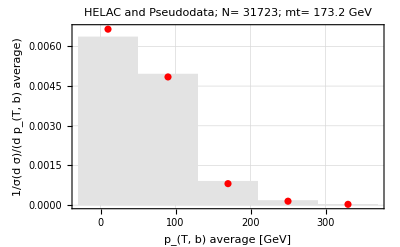

```mathematica
crossectionhel={1067.00,1040.40,1067.18,985.914,960.451};
filehel=Table[FileNames[][[i]],{i,1,nmass}];

datahel=Block[{list},
list=Reap[Do[Sow[ReadList[filehel[[i]],{Number, Number, Number, Number}]],{i,1,nmass,1}]]][[2,1]];
datahisthel[ndiffdist_]:=Partition[Reap[Do[Block[{datalist},
datalist=Sow[datahel[[j,i]]];
],{j,1,nmass,1},{i, start[ndiffdist],start[ndiffdist]+nbins-1,1}]][[2,1]],nbins](*contains set of all histogram data for mtt bar for 5 different mass*)
crossectionhel=Table[Reap[Do[Sow[datahel[[j,1]]],{j,1,nmass,1}]][[2,1,j,2]],{j,1,nmass}] (*fb*)

binshel=Partition[Block[{bin},
bin=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,1]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
binwidthel=Table[(Max[binshel[[i]]]-Min[binshel[[i]]])/(nbins-1),{i,1,5}];
binsrealhel=Reap[Do[Sow[Chop[binshel[[i]]-binwidthel[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsrealhel[[i]],Max[binsrealhel[[i]]]+binwidthel[[i]]]],{i,1,nmass,1}]][[2,1]];
bwrealhel=Table[(Max[binsrealhel[[i]]]-Min[binsrealhel[[i]]])/(nbins),{i,1,nmass}];

valsdatahel[numbofdiffdist_]:=Partition[Block[{val},
val=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,2]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
valsnhel[numbofdiffdist_]:=Table[valsdatahel[numbofdiffdist][[i]]/(crossectionhel[[i]]),{i,1,nmass}];(*normalised differential distribution : divided by 1/cross section *)

errordatahel[numbofdiffdist_]:=Partition[Block[{err},
err=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,3]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
errnhel[numbofdiffdist_]:=Table[errordatahel[numbofdiffdist][[i]]/(crossectionhel[[i]]),{i,1,nmass}];

HELAC (THEORETICAL) AVERAGE DATA LIST;
valssethel=Reap[Do[Sow[{Reap[Do[Sow[valsdatahel[numbofdiffdist1][[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[valsdatahel[numbofdiffdist2][[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
valshel=Table[Reap[Do[Sow[Mean[valssethel[[j]][[All,i]]]],{i,1,nbins,1}]][[2,1]],{j,1,nmass}];

valsnormsethel=Reap[Do[Sow[{Reap[Do[Sow[valsnhel[numbofdiffdist1][[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[valsnhel[numbofdiffdist2][[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
valsnormhel=Table[Reap[Do[Sow[Mean[valsnormsethel[[j]][[All,i]]]],{i,1,nbins,1}]][[2,1]],{j,1,nmass}];

errnormsethel=Reap[Do[Sow[{Reap[Do[Sow[errnhel[numbofdiffdist1][[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[errnhel[numbofdiffdist2][[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
errnormhel=Table[Reap[Do[Sow[Sqrt[(errnormsethel[[j,1,i]])^2+(errnormsethel[[j,2,i]])^2]],{i,1,nbins}]][[2,1]],{j,1,nmass}];

normalisationhel=Round[Table[Sum[valsnormhel[[j,i]],{i,1,Length[valsnormhel[[j]]]}]*binwidthel[[j]],{j,1,nmass}]]


REBINNING HELAC;
valsnormrebinhel=Table[Table[Sum[Partition[valsnormhel[[k]],(Round[nbins/rebin])][[j,i]],{i,1,Round[nbins/rebin]}]/(Round[nbins/rebin]),{j,1,rebin}],{k,1,nmass}];
binsrebinhel=Table[Table[First[Partition[binshel[[j]],Round[nbins/rebin]][[i]]],{i,1,rebin}],{j,1,nmass}];
bwrebinhel=Table[(Max[binsrebinhel[[i]]]-Min[binsrebinhel[[i]]])/(rebin-1),{i,1,nmass}];
binsrebinrealhel=Reap[Do[Sow[Chop[binsrebinhel[[i]]-bwrebinhel[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsrebinrealhel[[i]],Max[binsrebinrealhel[[i]]]+bwrebinhel[[i]]]],{i,1,nmass,1}]][[2,1]];
bwrebinrealhel=Table[(Max[binsrebinrealhel[[i]]]-Min[binsrebinrealhel[[i]]])/(rebin),{i,1,nmass}];
errnormrebinhel=Table[Table[Sum[Partition[errnormhel[[k]],(Round[nbins/rebin])][[j,i]],{i,1,Round[nbins/rebin]}]/(Round[nbins/rebin]),{j,1,rebin}],{k,1,nmass}];
normalisationrebinhel=Round[Table[Sum[valsnormrebinhel[[j,i]],{i,1,Length[valsnormrebinhel[[j]]]}]*bwrebinrealhel[[j]],{j,1,nmass}]]


Which[int==1,
binhelac=binsrebin;
valhelac=valsnormrebin;                 (*can be different data from helac, ex: from different scale*)
binhelacreal=binsrebinreal;
errorhelac=errnormrebin;
,
int==2,
binhelac=binsrebinhel;
valhelac=valsnormrebinhel;                 (*can be different data from helac, ex: from different scale*)
binhelacreal=binsrebinrealhel;
errorhelac=errnormrebinhel;
]
valhelac
errorhelac
pseudoerror[stdnevents,3,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin]

histfromhelac[nmass_,bwreal_]:=Histogram[WeightedData[binhelac[[nmass]],valhelac[[nmass]]],{Min[binhelacreal[[nmass]]],Max[binhelacreal[[nmass]]],bwreal[[nmass]]},PlotTheme->"Detailed",ChartBaseStyle->EdgeForm[None],ChartStyle->GrayLevel[0.89]]
histfromhelaclist[nmass_,bwreal_]:=HistogramList[WeightedData[binhelac[[nmass]],valhelac[[nmass]]],{Min[binhelacreal[[nmass]]],Max[binhelacreal[[nmass]]],bwreal[[nmass]]}]

combine[nevents_,nmass_,binw_,binsreal_,bwreal_,bins_,nbins_]:=Show[histfromhelac[nmass,bwreal],pseudoplot[nevents,3,binw,binsreal,bwreal,bins,nbins],
PlotTheme->"Detailed",
PlotLabel-> StringForm["HELAC and Pseudodata; N= ``; mt= `` GeV",nevents, mass[[nmass]]],
FrameLabel-> {StringForm["`` [GeV]",variable[[numbofdiffdist]]],StringForm["``",varnorm[[numbofdiffdist]]]}
]

pt1=combine[stdnevents,3,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,bwrebinreal,binsrebin,rebin]
```

```mathematica
THE  TOP MAS EXTRACTION PART;
```

```mathematica
FITTING THE VALUE OF DIFFERENTIAL VARIABLE FROM HELAC (THEORY) FOR EACH BIN FOR FIVE MASSES;
```

```mathematica
THEORETICAL VALUES AND ERRORS EXCEPT THE ZEROES ONE;
```

```mathematica
valsnormtheo=Reap[Do[Sow[valhelac[[All,i]]],{i,1,rebin,1}]][[2,1]]*(bwrebin[[1]]*rebin/npseudobin); (*the integrated value/area under the bar*)
errnormtheo=Reap[Do[Sow[errorhelac[[All,i]]],{i,1,rebin,1}]][[2,1]]*(bwrebin[[1]]*rebin/npseudobin);

valsbindata[int_]:=Reap[Do[Sow[{{mass[[i]],valsnormtheo[[int,i]]},ErrorBar[errnormtheo[[int,i]]]}],{i,1,nmass,1}]][[2,1]]; (*for graph*)
valsbindatanozero[nbins_]:=Reap[Block[{valerr,nol},
valerr=Table[valsbindata[i],{i,1,nbins}];
nol=Table[{{mass[[k]],0.},ErrorBar[0.]},{k,1,nmass}];
Sow[DeleteCases[valerr,nol]]]][[1]];

valsbintheo[int_]:=Reap[Do[Sow[{{mass[[i]],valsnormtheo[[int,i]]},errnormtheo[[int,i]]}],{i,1,nmass,1}]][[2,1]] (*{mass,vals},err*)
valsbintheonozero[nbins_]:=Reap[Block[{valerrtheo,nol},           (*{mass,vals},err NON ZERO BIN*)
valerrtheo=Table[valsbintheo[i],{i,1,nbins}];
nol=Table[{{mass[[k]],0.},0.},{k,1,nmass}];
Sow[DeleteCases[valerrtheo, nol]]]][[1]];

valsbindatanozero[rebin];
valsbintheonozero[rebin];
```

```mathematica
NON ZERO BIN ENTRIES;
```

```mathematica
nonzerobin=If[MemberQ[Flatten[Transpose[valsnormtheo]],0.]==False,{"nothing"},
Block[{valstheo,errtheo,zero,nonzero,all,comp},
valstheo=Transpose[valsnormtheo];
errtheo=Transpose[errnormtheo];
zero=Reap[Do[If[valstheo[[i,j]]== 0 && errtheo[[i,j]]== 0,
Sow[{i,j}],Nothing],{i,1,nmass,1},{j,1,rebin,1}]
][[2]];
all=Flatten[Table[{Range[nmass][[i]],Range[rebin][[j]]},{i,1,nmass},{j,1,rebin}],1];
comp=Complement[all,zero[[1]]];
nonzero=If[zero≠ {},Reap[Sow[comp]],
Nothing]
][[1]]
]
```

{nothing}

```mathematica
FITTING FUNCTIONS;
```

```mathematica
value[nbins_]:=Reap[Do[Sow[valsbintheonozero[nbins][[i]][[All,1]]],{i,1,Length[valsbintheonozero[nbins]],1}]][[2,1]];
err[nbins_]:=Reap[Do[Sow[valsbintheonozero[nbins][[i]][[All,2]]],{i,1,Length[valsbintheonozero[nbins]],1}]][[2,1]];
fitting[nbins_]:=LinearModelFit[value[nbins][[#]],fitf,x,Weights->1/(err[nbins][[#]])^2]&/@ Range[1,Length[value[nbins]]];

value[rebin];
err[rebin];
fitting[rebin];
```

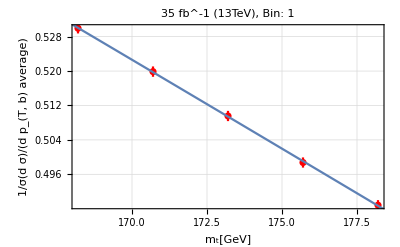
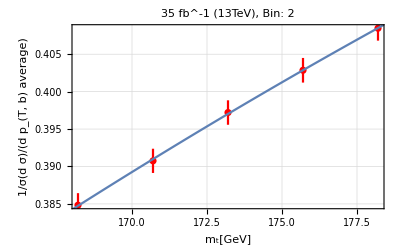
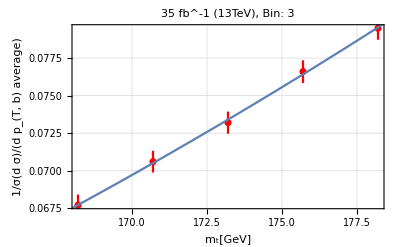
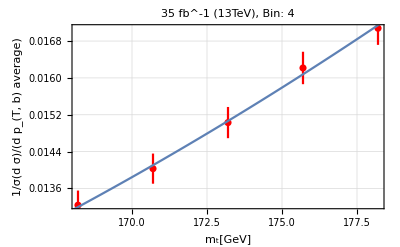
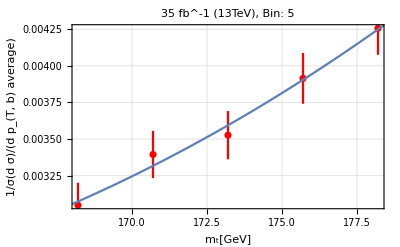

```mathematica
valsbinplot[int_,nbins_]:=ErrorListPlot[valsbindatanozero[nbins][[int]],PlotTheme->"Detailed",PlotLabel-> StringForm["`` fb^-1 (13TeV), Bin: ``",luminosity,int],PlotStyle->Red]
funcfit[int_,nbins_]:=Normal[fitting[nbins][[int]]]
funcbin[int_,nmass_,nbins_]:=funcfit[int,nbins]/.x-> mass[[nmass]]
combbinfunc[int_,nbins_]:=Block[{func},
func=funcfit[int,nbins]; (*fitting with polynomial arbitrary order*)
Show[valsbinplot[int,nbins],Plot[func,{x,160,180}],FrameLabel->{"m_t[GeV]",StringForm["``",varnorm[[numbofdiffdist]]]}]
]
allfit[nbins_]:=Table[combbinfunc[i,nbins],{i,1,Length[value[nbins]]}]

allfit[rebin]
```

```mathematica
PSEUDODATA VALUES AND ERRORS EXCEPT THE ZEROES ONE;
```

```mathematica
fact=(bwrebin[[1]]*rebin/npseudobin);

valsnormpseudo[nevents_,binw_,binsreal_,bins_,nbins_]:=Block[{valspseudo},
valspseudo=Reap[Do[Sow[pseudopointy[nevents,i,binw,binsreal,bins]*fact],{i,1,nmass,1}]][[2,1]];
Which[MemberQ[nonzerobin, "nothing"]==True,valspseudo,
MemberQ[nonzerobin, Nothing]==False,
Block[{logic},
logic=Partition[Reap[Do[
Sow[valspseudo[[nonzerobin[[i,1]],nonzerobin[[i,2]]]]],{i,1,Length[nonzerobin],1}]][[2,1]],Length[value[nbins]]] (*length value=non zero bins total*)
]
]
]
errnormpseudo[nevents_,binw_,binsreal_,bins_,nbins_]:=Block[{errpseudo},
errpseudo=Reap[Do[Sow[pseudoerror[nevents,i,binw,binsreal,bins,nbins]*fact],{i,1,nmass,1}]][[2,1]];
Which[MemberQ[nonzerobin, "nothing"]==True,errpseudo,
MemberQ[nonzerobin,Nothing]==False,
Block[{logic},
logic=Partition[Reap[Do[
Sow[errpseudo[[nonzerobin[[i,1]],nonzerobin[[i,2]]]]],{i,1,Length[nonzerobin],1}]][[2,1]],Length[value[nbins]]]
]
]
]

PSDATA USD FORG THE CHISQUARE;

valuep1=valsnormpseudo[stdnevents,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin][[number]];
errorp1=errnormpseudo[stdnevents,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin][[number]];
zeropost=Position[errorp1,0.]; 
errorp=Delete[errorp1,zeropost];
valuep=Delete[valuep1,zeropost];
(*pseudo data used only using the 173.2 GeV and dynamical Scale as the best theoretical prediction*)

valuep
errorp
```

{0.529303,0.392488,0.0620281,0.0126639,0.00286671}

{0.00280018,0.0027355,0.00136115,0.000591861,0.000274302}

```mathematica
THE χ^2 PROCEDURE;
```

167.988

{167.15,168.994}

0.921916

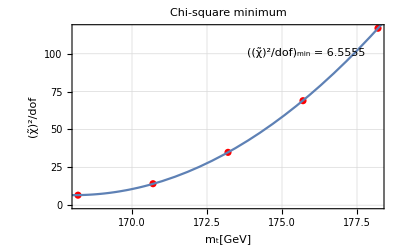

167.988±0.921916

```mathematica
CHI SQUARE STUFF;

chisquarebin[pvalue_,perror_,int_,mass_,nbins_]:=N[(pvalue[[int]]-fitting[nbins][[int]][mass])^2/(perror[[int]]^2)];
sumchisquare[pvalue_,perror_,mass_,nbins_]:=N[Sum[chisquarebin[pvalue,perror,i,mass,nbins],{i,1,Length[pvalue]-1}]];
chitilde[pvalue_,perror_,mass_,nbins_]:=N[sumchisquare[pvalue,perror,mass,nbins]/(Length[pvalue]-1)]
minchitilde[pvalue_,perror_,nbins_]:=x/.Last[FindMinimum[chitilde[pvalue,perror,x,nbins],{x,168.2,178.2}]]


chidata=ParallelTable[{mass[[j]],Table[chitilde[valuep,errorp,mass[[i]],rebin],{i,1,nmass}][[j]]},{j,1,nmass}];
minimumx=minchitilde[valuep,errorp,rebin];
minchi=chitilde[valuep,errorp,minimumx,rebin];
chivaluebnd=minchi+1;
chifunc=LinearModelFit[chidata,{1,x,x^2},x];
minimumx

deltamassbnd=x/.Solve[Normal[chifunc]==chivaluebnd,x] (*finding the corresponding m value for given chi square value without divide by dof*)
deltam1=Mean[Abs[minimumx-deltamassbnd]]

chiparabola=Show[ListPlot[chidata,FrameLabel-> {"m_t[GeV]","(χ̃)^2/dof"},PlotTheme->"Detailed",PlotStyle->Red],Plot[Normal[chifunc],{x,160,180}],PlotLabel->"Chi-square minimum",Epilog-> Inset[Framed[Style["((χ̃)^2/dof)_min = " <> ToString[minchi]],Background->White],Scaled[{.75,.85}]]]
PlusMinus[minimumx,deltam1]
```

```mathematica
BEFORE DIVIDED BY DEGREE OF FREEDOMS (EXTRACTING ONE DELTA MASS);
```

{{168.2,26.4079},{170.7,56.7106},{173.2,139.551},{175.7,276.048},{178.2,467.442}}

27.222

{167.682,168.461}

{0.305157,-0.473284}

0.389221

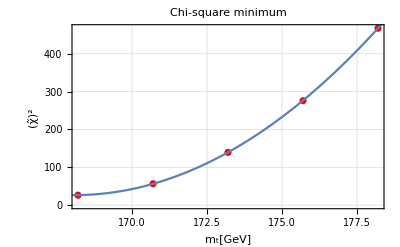

167.988±0.389221

```mathematica
minchitilderaw[pvalue_,perror_,nbins_]:=x/.Last[FindMinimum[sumchisquare[pvalue,perror,x,nbins],{x,168.2,178.2}]]

chidataraw=ParallelTable[{mass[[j]],Table[sumchisquare[valuep,errorp,mass[[i]],rebin],{i,1,nmass}][[j]]},{j,1,nmass}];
mmiddle=minchitilderaw[valuep,errorp,rebin];
minchiraw=sumchisquare[valuep,errorp,mmiddle,rebin];
chivaluebound=minchiraw+1;
chidataraw
chivaluebound
chifuncraw=LinearModelFit[chidataraw,{1,x,x^2},x];
deltamassbound=x/.Solve[Normal[chifuncraw]==chivaluebound,x] (*finding the corresponding m value for given chi square value without divide by dof*)
mmiddle-deltamassbound
deltamone=Mean[Abs[mmiddle-deltamassbound]]


chiparabolaraw=Show[ListPlot[chidataraw,FrameLabel-> {"m_t[GeV]","(χ̃)^2"},PlotTheme->"Detailed",PlotStyle->Red],Plot[Normal[chifuncraw],{x,160,180}],PlotLabel->"Chi-square minimum"]
PlusMinus[mmiddle,deltamone]
```

```mathematica
FITTED MASS ;
```

{163.174,165.506,167.346,171.29,172.859}

{1.39684,0.752842,0.177117,0.569257,0.518418}

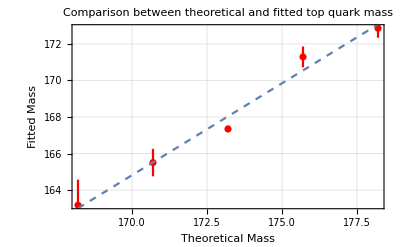

```mathematica
fittingmass[nevents_,binw_,binsreal_,bins_,nbins_,m_]:=Reap[
Block[{pvaluelist,perrorlist,zeropos,datachi,chisq,mout,result,chisqraw,datachiraw,fchiraw,chibound,deltambound,deltameins},
pvaluelist=valsnormpseudo[nevents,binw,binsreal,bins,nbins][[m]];
perrorlist=errnormpseudo[nevents,binw,binsreal,bins,nbins][[m]] ;
zeropos=Position[perrorlist,0.]; 
perrorlist=Delete[perrorlist,zeropos]; (*delete zero error values*)
pvaluelist=Delete[pvaluelist,zeropos];
chisq=ParallelTable[chitilde[pvaluelist,perrorlist,mass[[i]],nbins],{i,1,nmass}];
chisqraw=ParallelTable[sumchisquare[pvaluelist,perrorlist,mass[[i]],nbins],{i,1,nmass}];
datachi=ParallelTable[{mass[[j]],chisq[[j]]},{j,1,nmass}];
datachiraw=ParallelTable[{mass[[j]],chisqraw[[j]]},{j,1,nmass}];
fchiraw=LinearModelFit[datachiraw,{1,x,x^2},x];
mout=minchitilderaw[pvaluelist,perrorlist,nbins];
chibound=sumchisquare[pvaluelist,perrorlist,minchitilderaw[pvaluelist,perrorlist,nbins],nbins]+1;
deltambound=x/.Solve[Normal[fchiraw]==chibound,x];
deltameins=Mean[Abs[mout-deltambound]];
result=Sow[{mout,deltameins}]
]
][[2,1]];

massfit=Reap[Do[Sow[fittingmass[stdnevents,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin,i]],{i,1,nmass,1}]][[2,1]];
masschi=Reap[Do[Sow[Flatten[massfit[[i]],1]],{i,1,nmass,1}]][[2,1]];
fitmass=masschi[[All,1]]
fitmasserr=masschi[[All,2]]

PLOTTING THE THEORETICAL MASS AND THE MASS FROM CHI SQUARE + 1 ANALYSIS  FROM ONE PSEUDO EXPERIMENTS(NO BIASED);
fitmassplot=ErrorListPlot[Table[{{mass[[i]],fitmass[[i]]},ErrorBar[fitmasserr[[i]]]},{i,1,nmass}],PlotTheme->"Detailed",PlotStyle->Red];
fitmassfunc=Fit[Table[{mass[[i]],fitmass[[i]]},{i,1,nmass}],{1,x},x];
fittmass=Show[fitmassplot,Plot[fitmassfunc,{x,168.2,178.2},PlotStyle->Dashed],PlotTheme->"Detailed",FrameLabel-> { "Theoretical Mass","Fitted Mass"},PlotLabel-> "Comparison between theoretical and fitted top quark mass"]
```

```mathematica
N -PSEUDO EXPERIMENTS;
```

```mathematica
npseudoexp[nevents_,binw_,binsreal_,bins_,nbins_,n_]:=Partition[Reap[
For[k=1,k<n+1,k++,
Block[{pvaluelist,perrorlist,zeropos,datachi,chisq,mout,chisqmin,result,chisqminraw},
pvaluelist=valsnormpseudo[nevents,binw,binsreal,bins,nbins][[number]];
perrorlist=errnormpseudo[nevents,binw,binsreal,bins,nbins][[number]] ;
zeropos=Position[perrorlist,0.]; 
perrorlist=Delete[perrorlist,zeropos]; (*delete zero error values*)
pvaluelist=Delete[pvaluelist,zeropos];
chisq=ParallelTable[chitilde[pvaluelist,perrorlist,mass[[i]],nbins],{i,1,nmass}];
datachi=ParallelTable[{mass[[j]],chisq[[j]]},{j,1,nmass}];
mout=minchitilderaw[pvaluelist,perrorlist,nbins];
chisqmin=chitilde[pvaluelist,perrorlist,mout,nbins];
chisqminraw=sumchisquare[pvaluelist,perrorlist,mout,nbins];
result=Sow[{mout,chisqmin,chisqminraw}]
]
];
][[2,1]],n];

exp=Reap[Sow[npseudoexp[stdnevents,(bwrebin[[1]]*rebin/npseudobin),binsrebinreal,binsrebin,rebin,npseudo]]][[2,1,1,1]];
```

```mathematica
SOME STATISTICS AND  HISTOGRAMS ABOUT PSEUDO EXPERIMENT;
```

{1.68535,1.85948,1.98016,2.01677,2.04741,2.14188,2.35533,2.60075,2.60614,2.64569,2.68651,2.71048,2.80229,2.89954,2.92652,2.93762,2.94626,3.22521,3.35819,3.36034,3.398,3.53934,3.60234,3.62547,3.67592,3.72214,3.78382,3.79798,3.81761,3.91664,4.00162,4.10614,4.11988,4.17362,4.2131,4.2231,4.30591,4.34886,4.39385,4.39988,4.44081,4.59472,4.6275,4.65155,4.73279,4.73825,4.7764,4.83642,4.97961,4.98588,5.00223,5.01228,5.01777,5.04184,5.23086,5.25009,5.25666,5.28977,5.33601,5.38247,5.54669,5.57472,5.58432,5.60408,5.75512,6.14455,6.21513,6.26669,6.29529,6.48881,6.49385,6.57657,6.68755,6.74557,6.77743,6.79574,6.81267,6.93292,7.01513,7.17251,7.85315,7.90535,8.15748,8.16718,8.36811,8.49913,8.52486,9.0227,9.02497,9.0839,9.28908,9.4997,9.87969,11.1806,11.4132,11.8148,12.161,12.9515,13.3608,15.9138}

{{167.938,1.68535},{168.281,1.85948},{166.984,1.98016},{168.647,2.01677},{167.732,2.04741},{167.962,2.14188},{168.545,2.35533},{168.687,2.60075},{168.299,2.60614},{168.464,2.64569},{168.313,2.68651},{167.814,2.71048},{168.106,2.80229},{168.149,2.89954},{166.859,2.92652},{166.978,2.93762},{167.456,2.94626},{167.472,3.22521},{168.555,3.35819},{167.094,3.36034},{167.14,3.398},{167.523,3.53934},{166.655,3.60234},{167.704,3.62547},{167.868,3.67592},{167.779,3.72214},{166.971,3.78382},{167.756,3.79798},{168.064,3.81761},{167.989,3.91664},{167.902,4.00162},{167.474,4.10614},{167.723,4.11988},{167.325,4.17362},{168.145,4.2131},{168.472,4.2231},{168.165,4.30591},{168.587,4.34886},{168.85,4.39385},{167.193,4.39988},{169.377,4.44081},{168.484,4.59472},{167.396,4.6275},{168.027,4.65155},{167.211,4.73279},{167.222,4.73825},{168.943,4.7764},{168.633,4.83642},{168.069,4.97961},{167.406,4.98588},{167.023,5.00223},{168.512,5.01228},{168.415,5.01777},{168.095,5.04184},{168.698,5.23086},{168.517,5.25009},{167.573,5.25666},{167.211,5.28977},{168.443,5.33601},{166.796,5.38247},{167.328,5.54669},{167.292,5.57472},{167.795,5.58432},{167.841,5.60408},{167.49,5.75512},{167.562,6.14455},{167.768,6.21513},{167.877,6.26669},{168.687,6.29529},{167.37,6.48881},{168.321,6.49385},{167.912,6.57657},{168.379,6.68755},{169.454,6.74557},{167.937,6.77743},{167.666,6.79574},{167.475,6.81267},{168.455,6.93292},{168.494,7.01513},{168.739,7.17251},{168.516,7.85315},{169.017,7.90535},{167.748,8.15748},{168.345,8.16718},{168.302,8.36811},{167.267,8.49913},{169.1,8.52486},{167.065,9.0227},{168.297,9.02497},{167.4,9.0839},{168.948,9.28908},{167.691,9.4997},{169.213,9.87969},{169.382,11.1806},{169.585,11.4132},{169.609,11.8148},{168.663,12.161},{168.193,12.9515},{167.907,13.3608},{167.504,15.9138}}

100

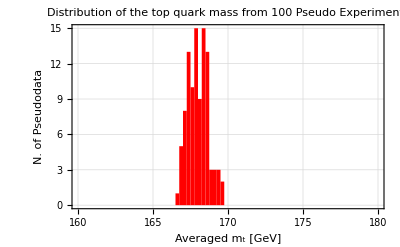

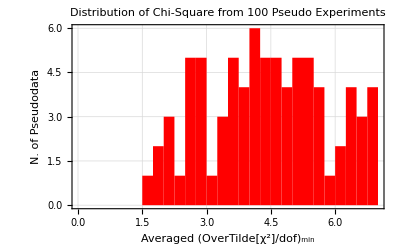

False

Theory, LO QCD | Variable | Luminosity [fb^-1] | m_t±δm_t[GeV] | Averaged ((χ̃)^2/dof)_min | Probability p-value | m_t^in-m_t^out [GeV]
Full, μ_0=mt | p_(T, b) average | 35 | 168.013±0.67401 | 5.59697 | 0.000167755 | 5.18737

```mathematica
(*pexpmass=Delete[Sort[exp[[All,1]]],Partition[(-1)*Range[4*npseudo/100],1]]; (*96 percent of the mass data *)
pexpchisq=Delete[Sort[exp[[All,2]]],Partition[(-1)*Range[4*npseudo/100],1]] (*96 percent of the chi square min data due to isolated big value of chi*)
*)
exp[[All,3]];

pexpchisq=Sort[exp[[All,2]]]

ELIMINATE THI  CHI-SQUARE THAT IS MORE THAN CHI SQUARE STANDARD FOR ET2;
chistandard=20;
newexp=Reap[Do[
Which[scalename[[k]]=="et2",
If[(pexpchisq[[i]]<chistandard)&&(pexpchisq[[i]]==exp[[j,2]]),Sow[{exp[[j,1]],exp[[j,2]]}],Nothing],
scalename[[k]]=="mt",
Nothing],
{k,1,Length[scalename],1},{i,1,Length[pexpchisq],1},{j,1,Length[exp],1}]][[2,1]]
Length[newexp]
pexpmass=newexp[[All,1]];
pexpchis=newexp[[All,2]];

massout=Mean[pexpmass];

deltamassout=Reap[Block[{sortedmass,variance},
sortedmass=pexpmass;
variance=Sort[Reap[Do[Sow[Abs[sortedmass[[i]]-Mean[sortedmass]]],{i,1,Length[sortedmass],1}]][[2,1]]]; (*sorted the spread of the data from the mean*)
Sow[variance[[Round[68*Length[sortedmass]/100]]]] (*take the 68% CL i.e take the 68%*Number-th of the data as the error*)
]][[2,1,1]];

chiout=Mean[pexpchis];

pexpmasshist=Histogram[pexpmass,{160,180,0.25},PlotTheme->"Detailed",FrameLabel->{"Averaged m_t [GeV]","N. of Pseudodata"},ChartBaseStyle->EdgeForm[None], ChartStyle->Red, PlotLabel-> "Distribution of the top quark mass from " <>ToString[Length[pexpchis]] " Pseudo Experiments"]
pexpchisqhist=Histogram[pexpchis,{0,7,0.25},PlotTheme->"Detailed",FrameLabel-> {"Averaged (OverTilde[χ^2]/dof)_min", "N. of Pseudodata"},ChartBaseStyle->EdgeForm[None], ChartStyle->Red,PlotLabel-> "Distribution of Chi-Square from " <>ToString[Length[pexpchis]]<>" Pseudo Experiments"]

SOME RESULTS;

pvalue[pvalue_]:= ChiSquarePValue[chiout*(Length[pvalue]-1),Length[pvalue]-1][[2]];
pvout=pvalue[valuep];
pvout>pvaluestandard
(*stddeviations=(Abs[massout[[number]]]*Sqrt[Length[pexpmass]/2])/InverseErfc[pvout]*10^-3*)
deltam=mass[[number]]-massout;
result=Grid[{{"Theory, LO QCD", "Variable","Luminosity [fb^-1]",ToString[PlusMinus[Subscript[m, t],Subscript[δm, t]],StandardForm]<>"[GeV]", "Averaged ((χ̃)^2/dof)_min","Probability p-value","m_t^in-m_t^out [GeV]"},
{StringForm["Full, μ_0=``",scale[[int]]],variable[[numbofdiffdist]],luminosity,PlusMinus[N[massout,2],N[deltamassout,2]],chiout,pvout ,deltam}},Frame->All]
```

```mathematica
EXPORTING FIGURES;
```

```mathematica
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_pseudodata"<>".pdf",pt1];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_pseudo_vs_theo_each_bin.pdf",allfit[rebin]];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_parabola_chi_square.pdf",chiparabola];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_pseudo_exp_mass_averaged.pdf", pexpmasshist];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_pseudo_exp_chi_square_averaged.pdf",pexpchisqhist];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_mass fitting.pdf", fittmass];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_rebin_"<>ToString[rebin]<>"_"<>ToString[luminosity]<>"_result_table.pdf", result];
```

```mathematica
If[luminosity==5,
Do[
Export["kdata_"<>ToString[varname[[numbofdiffdist]]]<>"_"<>ToString[rebin]<>"_"<>massname[[i]]<>"_"<>scalename[[int]]<>".txt",Transpose[{binsrebin[[i]],valhelac[[i]]}],"Table"],
{i,1,nmass,1}
],
Nothing
]
```

Nothing